# Discrete simplex

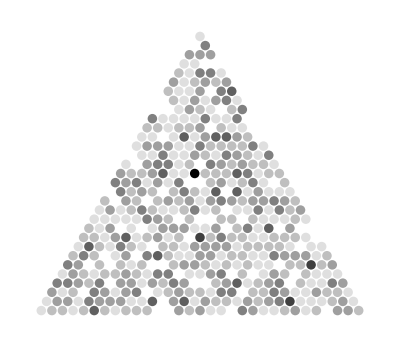
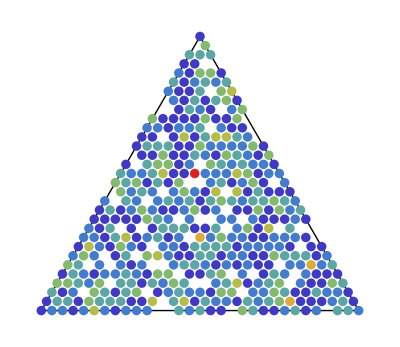
This is a notebook programmed to generate figures of discrete simplices like the ones below. 
-Graphics- | -Graphics- | 
The input is a distribution over the possible states of the system in the form of a .csv file in the same directory where this notebook lies. A state is defined as the number of agents that are using each of the 3 possible strategies, e.g. {23,45,32} is the state where 23 agents are using strategy 1, 45 agents are using strategy 2, and 32 agents are using strategy 3. The distribution over the possible states of the system is given as a .csv file, where each line represents the observation of a state, e.g.:
23,45,32
24,44,32
24,43,33
...
An example of this format for input files is given in accompanying file “data-without-frequencies.csv”. Using this format, it is assumed that each line is an observation (so there could be several repetitions of one line = state observation).

Alternatively, one can provide the frequency of each state, e.g.:
23,45,32, 0.012
24,44,32, 0.030
24,43,33, 0.034
....
An example of this second format for input files is given in accompanying file “data-with-frequencies.csv”. 

The output plot is saved in a pdf file with the same name as the .csv file provided as the input. Importantly, the plot produced by this notebook places strategy 1 on the bottom left, strategy 2 on the bottom right, and strategy 3 on the top. If you’d like to change this, the easiest way to do it is to change the order of the columns in the csv file.

## Parameters

```mathematica
nameOfFile="data-with-frequencies.csv";
(* There are more parameters at the beginning of section "Draw the simplex". They are not included here so we don't have to import the data again. *)
```

## Initialization

```mathematica
Simplex2DCoord[{x1_, x2_, x3_}] :=x1*{0, 0} + x2*{1, 0} + x3*{1/2, √3/2};
myDisk[center_List,radius_,p_]:=If[color,{ColorData["Rainbow"][p],Disk[center,radius]},{GrayLevel[1-p],Disk[center,radius]}]
```

## Import data

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import[nameOfFile];

If[Length[First[data]]==3,
(* The data does not contain the fraction of time each state has been observed, but it is just the time series of the states (e.g. {{8,11,11},{7,11,12}...}) *)
data=Tally[data];
data[[All,2]]=data[[All,2]]/Total[data[[All,2]]];
,
(* The data contains the fraction of time each state has been observed (e.g., {{8,11,11,0.001},{7,11,12,0.003}...}) *)
data=Map[List[#[[1;;3]],Last[#]]&,data];
];

Print["These are the first 10 elements of the distribution:\n",data[[;;10]]]
Print["These are states with a frequency greater than 0.01:\n",N[Select[data,Last[#]>0.01&]]]
Print["The maximum frequency is: ",N@Max[data[[All,2]]]]
```

These are the first 10 elements of the distribution:
{{{11,4,15},0.005},{{6,15,9},0.004},{{1,17,12},0.003},{{10,3,17},0.004},{{28,2,0},0.002},{{4,17,9},0.005},{{8,7,15},0.008},{{3,12,15},0.004},{{2,11,17},0.002},{{2,27,1},0.002}}

These are states with a frequency greater than 0.01:
{}

The maximum frequency is: 0.008

## Draw the simplex

```mathematica
color=True;
line=True;
separation=0.1;(*in between 0 and 1*)
lightness=1;(*in between 0 and 1*)

maxValue=Ceiling[Max[data[[All,2]]],0.001];
nAgents=Max[Flatten[data[[All,1]]]];
Print["The number of agents is: ",nAgents]
packedRadius=1/(2*nAgents);

g=Grid[{{
Graphics[{
If[line,Line[{{0, 0},{1,0},{1/2, √3/2},{0,0}}],##&[]],
Map[myDisk[Simplex2DCoord[First[#]/nAgents],packedRadius*(1-separation),(Last[#]^lightness)/maxValue]&,data]
},ImageSize->400]
,
DensityPlot[y^lightness,{x,0,.07},{y,0,1},ColorFunction->If[color,ColorData["Rainbow"],(GrayLevel[(1-#1)]&)],ColorFunctionScaling->False,AspectRatio->Automatic,Frame->True,FrameStyle->{{White,White},{White,White}},Axes->False,FrameTicksStyle->{Directive[Black,15],Thin},MaxRecursion->0,FrameTicks->{{None,Table[{ i,maxValue*i},{i,0,1,0.2}]},{None,None}},ImageSize->70]
}}]

SetDirectory[NotebookDirectory[]];
Export[StringDrop[nameOfFile,-4]<>".pdf",g];
```

The number of agents is: 30

-Graphics- | -Graphics-